```mathematica
SetDirectory@NotebookDirectory[];
```

## Data

```mathematica
model = 0;(*0:Depol;1:Deph;2:Damp;3:Coher;4:S-Q error*)
numQb=10;
numGt=numQb^2;
ϵ = 0.002;
SamSize=10000;
file = File["data/CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>"-r3.dat"];
Data = Import[file];
Data[[4]]
Data[[20]]
Data[[21]]
```

{seed:251084}

{Start,Time:,DateObject[{2020,,2,,18,,19,,21,,59.9963},,Instant,,Gregorian,,8.]}

{End,Time:,DateObject[{2020,,2,,19,,22,,32,,41.7347},,Instant,,Gregorian,,8.]}

## Error

667

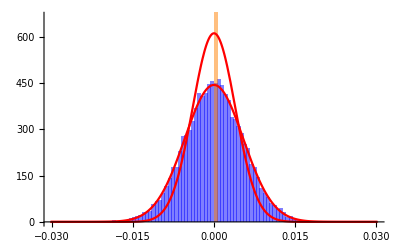

{-0.0000186884,0.0000295872,-4.43995×10^-9,2.72575×10^-9,-8.47672×10^-13,4.3414×10^-13,-5.91415×10^-18,9.94908×10^-17,1.22521×10^-19,2.9417×10^-20}

{-0.0000883065,0.0000156041,-2.75872×10^-6,4.87979×10^-7,-8.63606×10^-8,1.52916×10^-8,-2.709×10^-9,4.80157×10^-10,-8.51484×10^-11,1.51073×10^-11}

{0.0000543938,4.30156×10^-7,6.58878×10^-9,9.59485×10^-11,1.71512×10^-12,3.18807×10^-14,6.39558×10^-16,1.3174×10^-17,2.80139×10^-19,6.04275×10^-21}

{0.0000394922,6.98381×10^-6,1.23628×10^-6,2.19071×10^-7,3.88585×10^-8,6.89947×10^-9,1.22622×10^-9,2.18138×10^-10,3.88415×10^-11,6.92236×10^-12}

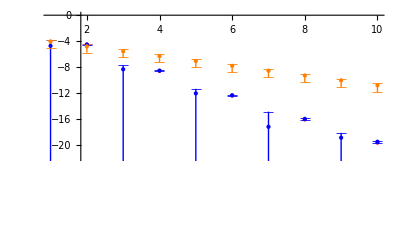

```mathematica
US=Data[[9]];
CS=Data[[15]];

scale=6;
xMax=Max[Abs[Join[US,CS,US,CS]]]/scale;
xMin=-xMax;
dx=(xMax-xMin)/100;
HUplot=Histogram[US,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
σ=Sqrt[Moment[US,2]];
yMax=Ceiling[1.5*SamSize*dx*PDF[NormalDistribution[0,σ],0]]
NDUplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
σ=Sqrt[Moment[CS,2]];
NDCplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
Show[HUplot,HCplot,NDUplot,NDCplot,PlotRange->{{xMin,xMax},{0,yMax}}]

Nσ=2;y0=10^-60;
MU=Table[Moment[US,m],{m,1,10,1}]
MC=Table[Moment[CS,m],{m,1,10,1}]
σMU=Table[Sqrt[(Moment[US,2*m]-Moment[US,m]^2)/SamSize],{m,1,10,1}]
σMC=Table[Sqrt[(Moment[CS,2*m]-Moment[CS,m]^2)/SamSize],{m,1,10,1}]
MUp=Abs[MU]+Nσ*σMU; MUm=Table[Max[{Abs[MU[[m]]]-Nσ*σMU[[m]],y0}],{m,1,10,1}];
MCp=Abs[MC]+Nσ*σMC; MCm=Table[Max[{Abs[MC[[m]]]-Nσ*σMC[[m]],y0}],{m,1,10,1}];

olU=Table[{MU[[m]]-Nσ*σMU[[m]],MU[[m]]+Nσ*σMU[[m]]}/((Abs[MU[[m]]]+Abs[MC[[m]]])/2),{m,1,3,1}];
olC=Table[{MC[[m]]-Nσ*σMC[[m]],MC[[m]]+Nσ*σMC[[m]]}/((Abs[MU[[m]]]+Abs[MC[[m]]])/2),{m,1,3,1}];

yMin =Floor[ Min[Join[Log10[Abs[MU]],Log10[Abs[MC]]]]]-2;
σ=Sqrt[Moment[US,2]];
MG=Table[(m-1)!!*σ^m,{m,1,10,1}]; logMG=Table[{m,Log10[MG[[m]]]},{m,2,10,2}];
MGplot=ListPlot[logMG,PlotStyle->{PointSize[Large],Red}];
MUplot=ListPlot[Log10[Abs[MU]],PlotStyle->{PointSize[Medium],Blue}];
MCplot=ListPlot[Log10[Abs[MC]],PlotStyle->{PointSize[Medium],Orange}];
σMUplot=ListPlot[{Log10[MUm],Log10[MUp]},PlotStyle->{Opacity[1,Blue],Opacity[1,Blue]},PlotMarkers->{"—","—"},Filling->{1->{2}},FillingStyle->Opacity[1,Blue]];
σMCplot=ListPlot[{Log10[MCm],Log10[MCp]},PlotStyle->{Opacity[1,Orange],Opacity[1,Orange]},PlotMarkers->{"—","—"},Filling->{1->{2}},FillingStyle->Opacity[1,Orange]];
Show[MGplot,σMUplot,σMCplot,MUplot,MCplot,PlotRange->{Full,{yMin,0}}]
```

## Fidelity

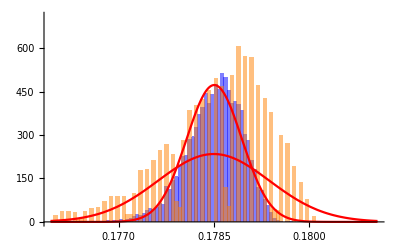

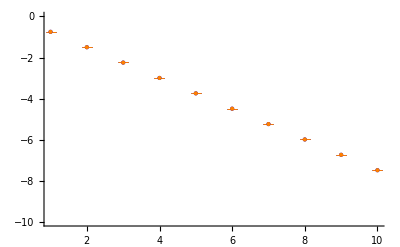

```mathematica
US=Data[[12]];
CS=Data[[18]];

scale=2;
μ=(Moment[US,1]+Moment[CS,1])/2;
xMax=μ+Max[Abs[Join[US-μ,CS-μ]]]/scale;
xMin=2μ-xMax;
dx=(xMax-xMin)/100;
HUplot=Histogram[US,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
μ=Moment[US,1];
σ=Sqrt[Moment[US,2]-μ^2];
yMax=Ceiling[1.5*SamSize*dx*PDF[NormalDistribution[0,σ],0]];
NDUplot=Plot[SamSize*dx*PDF[NormalDistribution[μ,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
μ=Moment[CS,1];
σ=Sqrt[Moment[CS,2]-μ^2];
NDCplot=Plot[SamSize*dx*PDF[NormalDistribution[μ,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
Show[HUplot,HCplot,NDUplot,NDCplot,PlotRange->{{xMin,xMax},{0,yMax}}]

MU=Table[Moment[US,m],{m,1,10,1}];
MC=Table[Moment[CS,m],{m,1,10,1}];
σMU=Table[Sqrt[(Moment[US,2*m]-Moment[US,m]^2)/SamSize],{m,1,10,1}];
σMC=Table[Sqrt[(Moment[CS,2*m]-Moment[CS,m]^2)/SamSize],{m,1,10,1}];
MUp=Abs[MU]+Nσ*σMU; MUm=Table[Max[{Abs[MU[[m]]]-Nσ*σMU[[m]],y0}],{m,1,10,1}];
MCp=Abs[MC]+Nσ*σMC; MCm=Table[Max[{Abs[MC[[m]]]-Nσ*σMC[[m]],y0}],{m,1,10,1}];

AppendTo[olU,{MU[[1]]-Nσ*σMU[[1]],MU[[1]]+Nσ*σMU[[1]]}/((Abs[MU[[1]]]+Abs[MC[[1]]])/2)];
AppendTo[olC,{MC[[1]]-Nσ*σMC[[1]],MC[[1]]+Nσ*σMC[[1]]}/((Abs[MU[[1]]]+Abs[MC[[1]]])/2)];

yMin =Floor[ Min[Join[Log10[Abs[MU]],Log10[Abs[MC]]]]]-2;
MUplot=ListPlot[Log10[Abs[MU]],PlotStyle->{PointSize[Medium],Blue}];
MCplot=ListPlot[Log10[Abs[MC]],PlotStyle->{PointSize[Medium],Orange}];
σMUplot=ListPlot[{Log10[MUm],Log10[MUp]},PlotStyle->{Opacity[1,Blue],Opacity[1,Blue]},PlotMarkers->{"—","—"},Filling->{1->{2}},FillingStyle->Opacity[1,Blue]];
σMCplot=ListPlot[{Log10[MCm],Log10[MCp]},PlotStyle->{Opacity[1,Orange],Opacity[1,Orange]},PlotMarkers->{"—","—"},Filling->{1->{2}},FillingStyle->Opacity[1,Orange]];
Show[σMUplot,σMCplot,MUplot,MCplot,PlotRange->{Full,{yMin,0}}]
```

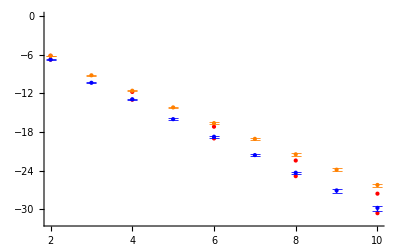

```mathematica
μ=Moment[US,1];
σ=Sqrt[Moment[US,2]-μ^2];
MG=Table[(m-1)!!*σ^m,{m,1,10,1}];logMG=Table[{m,Log10[MG[[m]]]},{m,2,10,2}];
MU=Table[Moment[US-μ,m],{m,1,10,1}];logMU=Table[{m,Log10[Abs[MU[[m]]]]},{m,2,10,1}];
σMU=Table[Sqrt[(Moment[US-μ,2*m]-Moment[US-μ,m]^2)/SamSize],{m,1,10,1}];
MUp=Abs[MU]+Nσ*σMU; MUm=Table[Max[{Abs[MU[[m]]]-Nσ*σMU[[m]],y0}],{m,1,10,1}];
logMUp=Table[{m,Log10[MUp[[m]]]},{m,2,10,1}];logMUm=Table[{m,Log10[MUm[[m]]]},{m,2,10,1}];

MGUplot=ListPlot[logMG,PlotStyle->{PointSize[Large],Red}];
MUplot=ListPlot[logMU,PlotStyle->{PointSize[Medium],Blue}];
σMUplot=ListPlot[{logMUm,logMUp},PlotStyle->{Opacity[1,Blue],Opacity[1,Blue]},PlotMarkers->{"—","—"},Filling->{1->{2}},FillingStyle->Opacity[1,Blue]];

μ=Moment[CS,1];
σ=Sqrt[Moment[CS,2]-μ^2];
MG=Table[(m-1)!!*σ^m,{m,1,10,1}];logMG=Table[{m,Log10[MG[[m]]]},{m,2,10,2}];
MC=Table[Moment[CS-μ,m],{m,1,10,1}];logMC=Table[{m,Log10[Abs[MC[[m]]]]},{m,2,10,1}];
σMC=Table[Sqrt[(Moment[CS-μ,2*m]-Moment[CS-μ,m]^2)/SamSize],{m,1,10,1}];
MCp=Abs[MC]+Nσ*σMC; MCm=Table[Max[{Abs[MC[[m]]]-Nσ*σMC[[m]],y0}],{m,1,10,1}];
logMCp=Table[{m,Log10[MCp[[m]]]},{m,2,10,1}];logMCm=Table[{m,Log10[MCm[[m]]]},{m,2,10,1}];

MGCplot=ListPlot[logMG,PlotStyle->{PointSize[Large],Red}];
MCplot=ListPlot[logMC,PlotStyle->{PointSize[Medium],Orange}];
σMCplot=ListPlot[{logMCm,logMCp},PlotStyle->{Opacity[1,Orange],Opacity[1,Orange]},PlotMarkers->{"—","—"},Filling->{1->{2}},FillingStyle->Opacity[1,Orange]];

yMin =Floor[ Min[Join[Log10[Abs[MU]],Log10[Abs[MC]]]]]-2;
Show[MGUplot,MGCplot,σMUplot,σMCplot,MUplot,MCplot,PlotRange->{Full,{yMin,0}}]
```

## Overlap

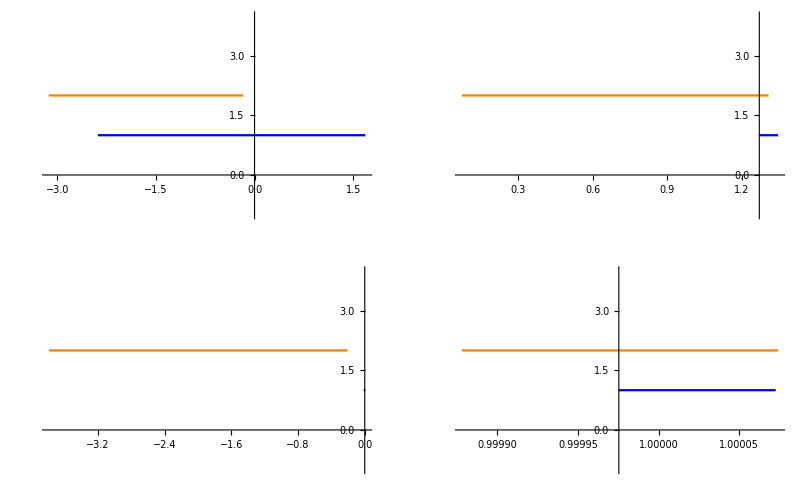

```mathematica
MUplot=Plot[1,{x,olU[[1,1]],olU[[1,2]]},PlotStyle->Blue];
MCplot=Plot[2,{x,olC[[1,1]],olC[[1,2]]},PlotStyle->Orange];
olplot1=Show[MUplot,MCplot,PlotRange->{Full,{-1,4}}];
MUplot=Plot[1,{x,olU[[2,1]],olU[[2,2]]},PlotStyle->Blue];
MCplot=Plot[2,{x,olC[[2,1]],olC[[2,2]]},PlotStyle->Orange];
olplot2=Show[MUplot,MCplot,PlotRange->{Full,{-1,4}}];
MUplot=Plot[1,{x,olU[[3,1]],olU[[3,2]]},PlotStyle->Blue];
MCplot=Plot[2,{x,olC[[3,1]],olC[[3,2]]},PlotStyle->Orange];
olplot3=Show[MUplot,MCplot,PlotRange->{Full,{-1,4}}];
MUplot=Plot[1,{x,olU[[4,1]],olU[[4,2]]},PlotStyle->Blue];
MCplot=Plot[2,{x,olC[[4,1]],olC[[4,2]]},PlotStyle->Orange];
olplot4=Show[MUplot,MCplot,PlotRange->{Full,{-1,4}}];
GraphicsGrid[{{olplot1,olplot2},{olplot3,olplot4}}]
```